```mathematica
f[w_,n_]:=(w+1)^-n+(t-w)^-n;
(*sigmak0:=(4π a0^2 α^4 nocc)/((betaT2+c betaB2)2bprime);
*)(*A1:=1/(t+1)(1+2tprime)/(1+tprime/2)^2;
A2:=(t-1)/2 bprime^2/(1+tprime/2)^2;
A3:=Log[betaT2/(1-betaT2)]-betaT2-Log[2bprime];*)

dσdw[w_]:=sigmak0(A3 f[w,3]+f[w,2]+(2 A2)/(t-1)-A1 f[w,1]);
σrel[T_]:=sigmak0(A3[T]/2(1-1/t[T]^2)+1-1/t[T]+A2[T]-A1[T]Log[t[T]]);
$Assumptions=_∈Reals;
```

```mathematica
Integrate[w dσdw[w],{w,e1,1/2},Assumptions->{0<e1<1/2,w>=0}]//FullSimplify
```

$Aborted

```mathematica
Integrate[w A3 f[w,3],{w,e1,1/2},Assumptions->{0<e1<1/2,w>=0}]
Integrate[w f[w,2],{w,e1,1/2},Assumptions->{0<e1<1/2,w>=0}]
Integrate[w (2 A2)/(t-1),{w,e1,1/2},Assumptions->{0<e1<1/2,w>=0}]
Integrate[-w A1 f[w,1],{w,e1,1/2},Assumptions->{0<e1<1/2,w>=0}]
```

ConditionalExpression[(A3 (1+2 e1-8 e1^2))/(18 (1+e1)^2)+(A3 (-2 e1 (1+2 e1 (-1+t))+t))/(2 (1-2 t)^2 (e1-t)^2), e1>t||2 t>1]

ConditionalExpression[2/3-1/(1+e1)+e1/(e1-t)+1/(-1+2 t)+Log[3/2]-Log[1+e1]+Log[-1/2+t]-Log[-e1+t], t>1/2]

(2 A2 (1/8-e1^2/2))/(-1+t)

ConditionalExpression[-A1 (Log[(2 (1+e1))/3]+t Log[(2 (-e1+t))/(-1+2 t)]), e1>t]

```mathematica
Integrate[t(1/t^2+1/(1-t)^2+((γ-1)/γ)^2-(2γ-1)/γ^2 1/(t(1-t))),{t,e1,1/2},Assumptions->{0<e1<1/2}]//FullSimplify
```

-((-1+2 e1) (-1-e1 (-1+γ)^2+2 e1^2 (-1+γ)^2+(2-9 γ) γ))/(8 (-1+e1) γ^2)+(-1+1/γ^2-2/γ) Log[2-2 e1]-Log[2 e1]

```mathematica
Integrate[(1/t^2),{t,e1,1/2},Assumptions->{0<e1<1/2}]//FullSimplify
Integrate[(1/(1-t)^2),{t,e1,1/2},Assumptions->{0<e1<1/2}]//FullSimplify
Integrate[(((γ-1)/γ)^2),{t,e1,1/2},Assumptions->{0<e1<1/2}]//FullSimplify
Integrate[(-(2γ-1)/γ^2 1/(t(1-t))),{t,e1,1/2},Assumptions->{0<e1<1/2}]//FullSimplify
```

-2+1/e1

2+1/(-1+e1)

((1/2-e1) (-1+γ)^2)/γ^2

((1-2 γ) Log[-1+1/e1])/γ^2

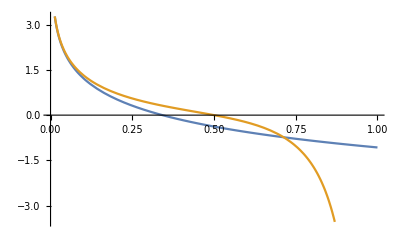

```mathematica
With[{g=1.1,γ=1.1},Plot[{Log[1/(4e1)]+1-(2g-1)/g^2 Log[2]+1/8((g-1)/g)^2,(-Log[2 e1]+2+1/(e1-1)-Log[2-2 e1]-((4 e1^2-1) (γ-1)^2)/(8 γ^2)+((1-2 γ) Log[2-2 e1])/γ^2)},{e1,0,1}]]
```

```mathematica
Integrate[t Integrate[(1/t^2+1/(1-t)^2+((γ-1)/γ)^2-(2γ-1)/γ^2 1/(t(1-t))),t],{t,0,e1},Assumptions->{0<=e1<1/2}]
```

1/(6 γ^2)((3-6 γ-6 γ^2+e1^2 (-3+6 γ)) Log[1-e1]+e1 (3+2 e1^2 (-1+γ)^2-6 γ-12 γ^2+e1 (3-6 γ) Log[e1]))

```mathematica
Integrate[t(1/(1-t)^2),t,Assumptions->{0<e1<1/2}]
```

-1/(-1+t)+Log[-1+t]